```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\packages\\force_toolbox.wl"]
```

```mathematica
clong = 3;(*Number of hourglass columns, c≥2*)
rlong =5; (*Number fo hourglass rows, r≥1*)
nrlong = (4*clong+2); (*Rods per row*)
nlong = nrlong*rlong ;

cshort = 5;(*Number of hourglass columns, c≥2*)
rshort =3; (*Number fo hourglass rows, r≥1*)
nrshort = (4*cshort+2); (*Rods per row*)
nshort = nrshort*rshort ;
long = 1;
short = 0.8;

rodlengths = ConstantArray[1,nlong];

Graphics[Join[Last@BuildStructure[clong,rlong,rodlengths]]]
```

Part::span: 1;;nr is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 3 of {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«20»}⟦1;;nr⟧ does not exist.

Part::partw: Part 4 of {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«20»}⟦1;;nr⟧ does not exist.

Part::span: 1;;nr is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 4 of {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«20»}⟦1;;nr⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;nr is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

$Aborted

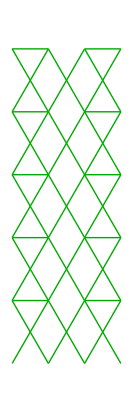

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =5; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;

rodlengths = ConstantArray[1,n];
(*Number of rods*)Graphics[Join[Last@BuildStructure[c,r,rodlengths]],PlotRange->{0,9}]
```

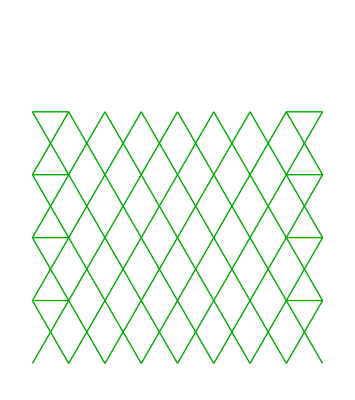

```mathematica
c = 8;(*Number of hourglass columns, c≥2*)
r =4; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;

rodlengths = ConstantArray[1,n];
(*Number of rods*)Graphics[Join[Last@BuildStructure[c,r,rodlengths]],PlotRange->{0,9}]
```

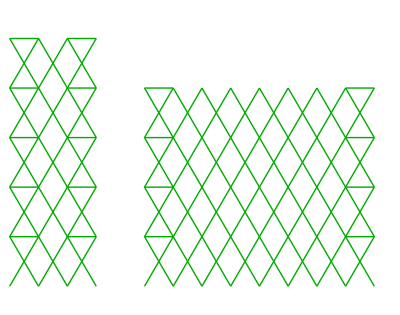

```mathematica
GraphicsRow[{-Graphics-,-Graphics-}]
```

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =90; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;(*Number of rods*)
```

```mathematica
(*rodlengths = RandomChoice[{0.95,1},n];*)

long =1;
short =0.96;

(*leftturn = Join[ConstantArray[short,2*c/3],
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*botrow*)
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*midrow*)
{long,long},
{long,long}]; *)
leftturn = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{short,short},
{long,long}]; (*right hand top tip*)

rightturn = Join[ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{long,long},
{short,short}]; (*right hand top tip*)

short = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{short,long},
{long,short}]; (*right hand top tip*)

long= Join[ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{long,long},
{long,long}]; (*right hand top tip*)

(*rodlengths= Join[leftturn,leftturn];*)
(*rodlengths= Join[rightturn,rightturn];*)
(*rodlengths= Join[short,short];*)

(*rodlengths= Flatten[RandomChoice[{leftturn,rightturn},r]];*)

(*rodlengths= Flatten[ConstantArray[leftturn,r]];*)
```

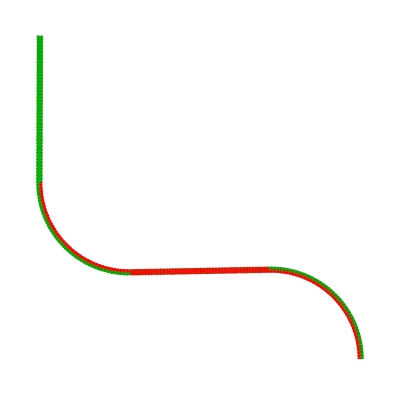

```mathematica
rodlengths= Flatten[Join[ConstantArray[leftturn,r/4],ConstantArray[short,r/4],ConstantArray[rightturn,r/4],ConstantArray[long,r/4]]];
Graphics[Join[Last@BuildStructure[c,r,rodlengths]]]
```

```mathematica
c = 9;(*Number of hourglass columns, c≥2*)
r =70; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;(*Number of rods*)
```

```mathematica
(*rodlengths = RandomChoice[{0.95,1},n];*)

long =1;
short =0.88;

(*leftturn = Join[ConstantArray[short,2*c/3],
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*botrow*)
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*midrow*)
{long,long},
{long,long}]; *)
leftturn = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{short,short},
{long,long}]; (*right hand top tip*)

rightturn = Join[ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{long,long},
{short,short}]; (*right hand top tip*)

short = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{short,long},
{long,short}]; (*right hand top tip*)

long= Join[ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{long,long},
{long,long}]; (*right hand top tip*)

(*rodlengths= Join[leftturn,leftturn];*)
(*rodlengths= Join[rightturn,rightturn];*)
(*rodlengths= Join[short,short];*)

(*rodlengths= Flatten[RandomChoice[{leftturn,rightturn},r]];*)

(*rodlengths= Flatten[ConstantArray[leftturn,r]];*)
```

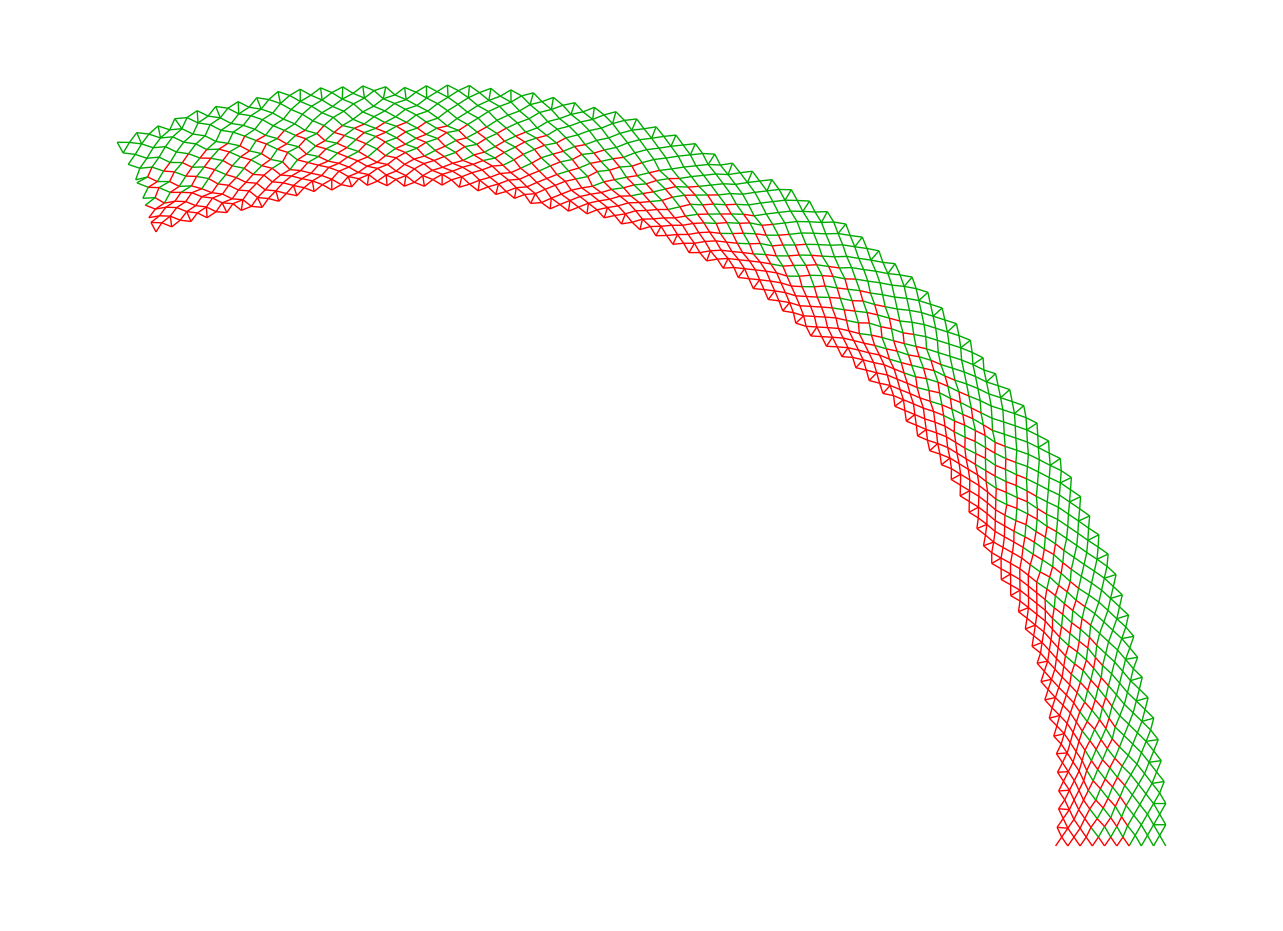

```mathematica
rodlengths= Flatten[Join[ConstantArray[leftturn,r]]];
Graphics[Join[Last@BuildStructure[c,r,rodlengths]]]
```